### Discontinuous Galerkin Method for Rank 2

```mathematica
switch[x_]:=If[x>0,x,0];
```

```mathematica
legendre[n_,x_]:=LegendreP[n-1,2 x-1] √(2 (n-1)+1)
```

```mathematica
f11[x_]:=If[Abs[x]>1,0,If[x≥0,1/(√2),-1/(√2)]]
f21[x_]:=If[Abs[x]>1,0,If[x≥0,√(3/2) (-1+2 x),f21[-x]]]
f22[x_]:=If[Abs[x]>1,0,If[x≥0,√(1/2) (-2+3 x),-f22[-x]]]
f31[x_]:=If[Abs[x]>1,0,If[x≥0,1/3 √(1/2) (1-24 x+30 x^2),-f31[-x]]]
f32[x_]:=If[Abs[x]>1,0,If[x≥0,1/2 √(3/2) (3-16 x+15 x^2),f32[-x]]]
f33[x_]:=If[Abs[x]>1,0,If[x≥0,1/3 √(5/2) (4-15 x+12 x^2),-f33[-x]]]
```

```mathematica
f2[fnumber_]:=Which[fnumber==1,f21,fnumber==2,f22]
f3[fnumber_]:=Which[fnumber==1,f31,fnumber==2,f32,fnumber==3,f33]
```

```mathematica
v2[fnumber_,level_,place_]:=If[level==0,legendre[fnumber,#1]&,2^(level/2) f2[fnumber][2^level #1-(2 place-1)]&]
```

```mathematica
innerProduct[f_,g_,level_,place_]:=NIntegrate[f[x] g[x],{x,(place-1) 2^(-switch[level-1]),place 2^(-switch[level-1])}]
```

```mathematica
iterate2[n_]:=Module[{fnumber,level,place,hashMap,count},hashMap=Table[0,{i,1,2 2^n}];count=1;For[level=0,level≤n,level++,For[place=1,place≤2^switch[level-1],place++,For[fnumber=1,fnumber≤2,fnumber++,hashMap⟦count++⟧={fnumber,level+1,place}]]];Return[hashMap];]

getCoefficients2[f_,fnumber_,level_,place_]:=innerProduct[f,v2[fnumber,level,place],level,place]
```

```mathematica
fullCoefficients2[f_,n_]:=Module[{iters,i,hash,count,coeff},
iters=iterate2[n];
hash=Table[0,{i,1,Length[iters]}];
For[i=1,i≤Length[iters],i++,
coeff=getCoefficients2[f,iters⟦i⟧⟦1⟧,iters⟦i⟧⟦2⟧-1,iters⟦i⟧⟦3⟧];hash⟦i⟧=iters⟦i⟧->coeff;];Return[SparseArray[hash]]]

reconstruct2[coeffs_,x_,n_]:=Module[{fnumber,level,place,value},
value=0;
For[level=0,level≤n,level++,
For[place=1,place≤2^switch[level-1],place++,
For[fnumber=1,fnumber≤2,fnumber++,
value+=coeffs⟦fnumber,level+1,place⟧ v2[fnumber,level,place][x];
]]];Return[value]]
```

### Discontinuous Galerkin Calculation

```mathematica
coeffs2=fullCoefficients2[Sin[Pi #]&,4]//Quiet
```

SparseArray[<32>, {2, 5, 8}]

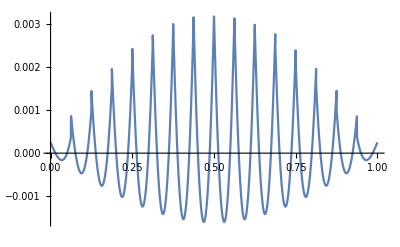

```mathematica
Plot[reconstruct2[coeffs2,x,4]-Sin[Pi x],{x,0,1}]
```

```mathematica
dg2Error=Table[Sqrt[.0062 Sum[(reconstruct2[#,x,n]-Sin[Pi x])^2,{x,0,1,.0062}]&@fullCoefficients2[Sin[Pi #]&,n]],{n,1,8}];
```

$Aborted

```mathematica
dg2Error={0.06321975749837573,0.015956037746255557,0.004019190773401819,0.0010041637908556752,0.00024756694313490845,0.00006357018311763907,0.000015868873869289,3.967025679859029*^-6}
```

{0.0632198,0.015956,0.00401919,0.00100416,0.000247567,0.0000635702,0.0000158689,3.96703×10^-6}

### Standard Definitions in the Old Hat Method

```mathematica
ϕ[x_]:=If[Abs[x]>1,0,1-Abs[x]]
ϕ[l_,i_]:=(ϕ[2^l(#-2^-l(2i-1))]&)
ceil[x_]:=1+Floor[x]

test[x_]:=Sin[Pi x]^2
```

```mathematica
getCoefficient[f_,x_,l_]:=f[x]-1/2 f[x+2^-l]-1/2 f[x-2^-l]
fullCoefficients[f_,l_]:={{f[1],f[0]}}~Append~Table[Table[getCoefficient[f,2^-k i,k],{i,1,2^k-1,2}],{k,1,l}]
Reconstruct[coefficients_]:=If[#==1,coefficients[[1,1]],
coefficients[[1,1]]#+coefficients[[1,2]](1-#)+Sum[coefficients[[2,l,ceil[2^(l-1)#]]] ϕ[2^l(#-2^-l(2ceil[2^(l-1)#]-1))],{l,1,Length[coefficients[[2]]]}]]&

project[f_,l_]:=Reconstruct[fullCoefficients[f,l]]
```

### Hat Error

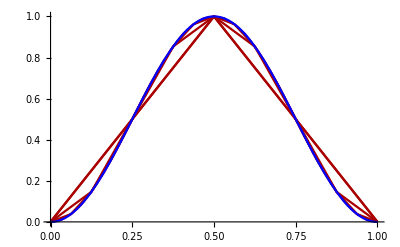

```mathematica
Show[Plot[Table[#[[i]][x],{i,1,5}],{x,0,1},PlotStyle->{Darker[Red]}]&[Table[project[test,n],{n,1,5}]],Plot[test[x],{x,0,1},PlotStyle->Blue]]
```

```mathematica
hatError=Table[Sqrt[.0062Sum[(Sin[Pi x]-Reconstruct[#][x])^2,{x,0,1,.0062}]&@fullCoefficients[Sin[Pi #]&,n]],{n,1,8}]
```

{0.150877,0.0392844,0.00992096,0.00248656,0.000622133,0.000155528,0.0000388839,9.72104×10^-6}

### Comparison of Errors:

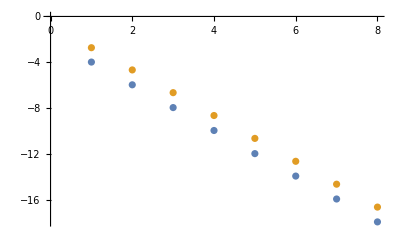

```mathematica
ListPlot[{dgError,hatError}//Log2]
```